# Quantum Algorithms: Introduction

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

```mathematica
Off[Measurement::nonum]
```

"Table of Contents"

## Quantum Teleportation

When one has access to both qubits, a SWAP gate for example is enough to send state from one qubit to the other.

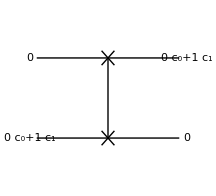

```mathematica
Let[Complex,c]
qc=QuantumCircuit[{Ket[S@{1}],ProductState[S[2]->{c[0],c[1]}]},SWAP[S[1],S[2]],{Ket[S@{2}],ProductState[S[1]->{c[0],c[1]}]},"PortSize"->2]
```

```mathematica
out=KetFactor[ExpressionFor[qc],S@{1,2}]
```

(c_0 0_S_1+c_1 1_S_1)⊗0_S_2

### Nonlocality in Entanglement

This is the quantum entangler circuit. It generates a maximally entagnled state.

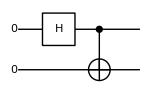

```mathematica
qc=QuantumCircuit[Ket[S@{1,2}],S[1,6],CNOT[S[1],S[2]]]
```

Here is the output state. It is indeed a maximally entangled state.

```mathematica
vec=ExpressionFor[qc]
```

(0_S_10_S_2)/(√2)+(1_S_11_S_2)/(√2)

Now Bob measure on his qubit.

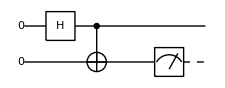

```mathematica
qc2=QuantumCircuit[qc,"Spacer",Measurement@S[2,3]]
```

This shows that the measurement outcome is just random.

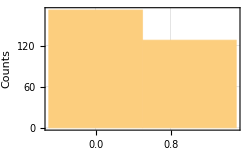

```mathematica
val=Table[Elaborate[qc2];Readout[S[2,3]],{300}];
Histogram[val,FrameLabel->{"Measurement Readout","Counts"}]
```

Here Alice, possessing the first qubit, measures her qubit before Bob measures his qubit.

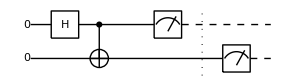

```mathematica
qc3=QuantumCircuit[qc,"Spacer",Measurement@S[1,3],"Separator",Measurement@S[2,3]]
```

This shows that the measurement outcomes of Alice’s and Bobs’ are perfectly correlated. This illustrates that Bob’s measurement results have affected by Alice measurement.

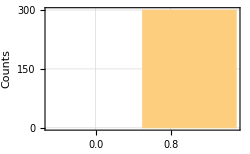

```mathematica
val=Boole@Table[Elaborate[qc3];Equal@@Readout[S[{1,2},3]],{300}];
Histogram[val,{-0.5,1.5,1},FrameLabel->{"Bob's readout equal to Alice's","Counts"}]
```

### Implementation of Quantum Teleportation

Here is a simulation of the quantum teleportation protocol using Q3.

The initial state of the total system at the beginning of the protocol.

```mathematica
Let[Complex,ψ]
vec=Ket[]ψ[0]+Ket[S[3]->1]ψ[1]//KetRegulate
```

0_S_3 ψ_0+1_S_3 ψ_1

```mathematica
tot=BellState[S@{0,2},0]**vec
```

(0_S_00_S_20_S_3 ψ_0)/(√2)+(1_S_01_S_20_S_3 ψ_0)/(√2)+(0_S_00_S_21_S_3 ψ_1)/(√2)+(1_S_01_S_21_S_3 ψ_1)/(√2)

The total state is rewritten in the Bell basis for qubits S[2,$] and S[3,$].

```mathematica
bs=BellState[S@{2,3}];
prj=Dyad[#,#,S@{2,3}]&/@bs;
KetFactor/@(prj**tot)//TableForm
```

((0_S_20_S_3+1_S_21_S_3)⊗(0_S_0 ψ_0+1_S_0 ψ_1))/(2 √2)
((0_S_21_S_3+1_S_20_S_3)⊗(1_S_0 ψ_0+0_S_0 ψ_1))/(2 √2)
((-0_S_21_S_3+1_S_20_S_3)⊗(1_S_0 ψ_0-0_S_0 ψ_1))/(2 √2)
((0_S_20_S_3-1_S_21_S_3)⊗(0_S_0 ψ_0-1_S_0 ψ_1))/(2 √2)

Step 1. Alice and Bob generates an entangled pair. Bob prepares a quantum state in a separate qubit.

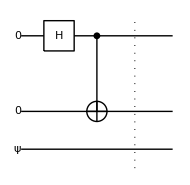

```mathematica
qc1=QuantumCircuit[Ket[S@{1,2}],ProductState[S[3]->{ψ[0],ψ[1]},"Label"->Ket[ψ]],S[1,6],CNOT[S[1],S[2]],"Separator","Invisible"->S[1.5]]
```

Step 2. Bob performs a Bell measurement on his qubits. This can be done by reversing the entangler circuit.

```mathematica
qc2a=QuantumCircuit[CNOT[S[2],S[3]],S[2,6]];
op=ExpressionFor[qc2a];
bs=BellState[S@{2,3}];
ls=op**bs;
Transpose@Thread[bs->ls]//TableForm
```

(0_S_20_S_3+1_S_21_S_3)/(√2)→0_S_20_S_3
(0_S_21_S_3+1_S_20_S_3)/(√2)→0_S_21_S_3
(0_S_21_S_3-1_S_20_S_3)/(√2)→1_S_21_S_3
(0_S_20_S_3-1_S_21_S_3)/(√2)→1_S_20_S_3

This is the corresponding quantum circuit model.

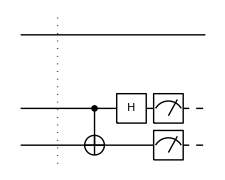

```mathematica
qc2=QuantumCircuit["Separator",qc2a,Measurement@S[{2,3},3],"Visible"->S[1],"Invisible"->S[1.5]]
```

Step 3. Bob sends the measurement outcome to Alice through a classical channel.
Step 4. Alice applies a proper unitary gate on her qubit in accordance with Bob’s message. These two steps are simulated by a feedback control.

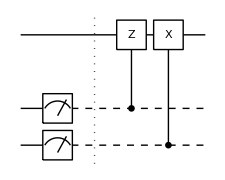

```mathematica
qc2=QuantumCircuit[Measurement@S[{2,3},3],"Separator",ControlledGate[S[2],S[1,3]],ControlledGate[S[3],S[1,1]],"Invisible"->S[1.5]]
```

Combining all the steps, one can transmit a quantum state to a remote party without a quantum channel.

```mathematica
in:=ProductState[S[3]->{ψ[0],ψ[1]},"Label"->Ket[ψ]];qc:=QuantumCircuit[in,Ket[S@{1,2}],S[1,6],CNOT[S[1],S[2]],"Separator","Spacer",CNOT[S[2],S[3]],S[2,6],Measurement[S[{2,3},3]],"Separator",ControlledGate[S[2],S[1,3]],ControlledGate[S[3],S[1,1]],ProductState[S[1]->{ψ[0],ψ[1]},"Label"->Ket[ψ]],"Invisible"->S[1.5]]
```

Check the result.

```mathematica
out=ExpressionFor[qc]/.{Conjugate[ψ[0]]*ψ[0]+Conjugate[ψ[1]]*ψ[1]->1};
KetFactor[out,S@{2,3}]
```

1_S_21_S_3⊗(1/2 (0_S_1 ψ[0]+1_S_1 ψ[1]))

Try with an explicit numbers as well.

```mathematica
{ψ[0],ψ[1]}=Normalize@{1,I*2};
out=ExpressionFor[qc];
in->KetFactor[out,S@{2,3}]//ExpandAll
```

(0/(√5)+(2 ⅈ 1)/(√5))_S_3→1_S_21_S_3⊗((0_S_1)/(√5)+(2 ⅈ 1_S_1)/(√5))

## Deutsch-Jozsa Algorithm

### Quantum Oracle

Here is a simple example, which is used in the Deutsch-Jozsa algorithm.

Consider a balanced function f as a classical oracle.

```mathematica
Clear[f];
f[0,0]=f[1,1]=0;
f[0,1]=f[1,0]=1;
```

Here is the corresponding quantum oracle.

```mathematica
cc=S@{1,2};
tt=S[3];
qc=QuantumCircuit[Oracle[f,cc,tt]]
```

-Graphics-

```mathematica
op=ExpressionFor[qc]
```

1/2+1/2 S_1^zS_2^z-1/2 S_1^zS_2^zS_3^x+S_3^x/2

```mathematica
bs=Basis@Join[cc,{tt}]
```

{0_S_10_S_20_S_3,0_S_10_S_21_S_3,0_S_11_S_20_S_3,0_S_11_S_21_S_3,1_S_10_S_20_S_3,1_S_10_S_21_S_3,1_S_11_S_20_S_3,1_S_11_S_21_S_3}

```mathematica
out=op**bs
```

{0_S_10_S_20_S_3,0_S_10_S_21_S_3,0_S_11_S_21_S_3,0_S_11_S_20_S_3,1_S_10_S_21_S_3,1_S_10_S_20_S_3,1_S_11_S_20_S_3,1_S_11_S_21_S_3}

```mathematica
Thread[bs->out]//TableForm
```

0_S_10_S_20_S_3→0_S_10_S_20_S_3
0_S_10_S_21_S_3→0_S_10_S_21_S_3
0_S_11_S_20_S_3→0_S_11_S_21_S_3
0_S_11_S_21_S_3→0_S_11_S_20_S_3
1_S_10_S_20_S_3→1_S_10_S_21_S_3
1_S_10_S_21_S_3→1_S_10_S_20_S_3
1_S_11_S_20_S_3→1_S_11_S_20_S_3
1_S_11_S_21_S_3→1_S_11_S_21_S_3

Let us consider another example, which is used in Simon’s algorithm.

Consider a two-to-one function as a classical oracle.

```mathematica
Clear[f];
f[0,0]=f[1,1]={0,1};
f[0,1]=f[1,0]={1,1};
```

Here is an implementation of the corresponding quantum oracle.

```mathematica
cc=S@{1,2};
tt=S@{3,4};
qc=QuantumCircuit[Oracle[f,cc,tt]]
```

-Graphics-

```mathematica
op=Elaborate@Oracle[f,cc,tt]
```

1/2 S_3^xS_4^x+1/2 S_1^zS_2^zS_4^x-1/2 S_1^zS_2^zS_3^xS_4^x+S_4^x/2

```mathematica
bs=Basis@Join[cc,tt]
```

{0_S_10_S_20_S_30_S_4,0_S_10_S_20_S_31_S_4,0_S_10_S_21_S_30_S_4,0_S_10_S_21_S_31_S_4,0_S_11_S_20_S_30_S_4,0_S_11_S_20_S_31_S_4,0_S_11_S_21_S_30_S_4,0_S_11_S_21_S_31_S_4,1_S_10_S_20_S_30_S_4,1_S_10_S_20_S_31_S_4,1_S_10_S_21_S_30_S_4,1_S_10_S_21_S_31_S_4,1_S_11_S_20_S_30_S_4,1_S_11_S_20_S_31_S_4,1_S_11_S_21_S_30_S_4,1_S_11_S_21_S_31_S_4}

```mathematica
out=op**bs
```

{0_S_10_S_20_S_31_S_4,0_S_10_S_20_S_30_S_4,0_S_10_S_21_S_31_S_4,0_S_10_S_21_S_30_S_4,0_S_11_S_21_S_31_S_4,0_S_11_S_21_S_30_S_4,0_S_11_S_20_S_31_S_4,0_S_11_S_20_S_30_S_4,1_S_10_S_21_S_31_S_4,1_S_10_S_21_S_30_S_4,1_S_10_S_20_S_31_S_4,1_S_10_S_20_S_30_S_4,1_S_11_S_20_S_31_S_4,1_S_11_S_20_S_30_S_4,1_S_11_S_21_S_31_S_4,1_S_11_S_21_S_30_S_4}

```mathematica
tbl=Thread[Rule[bs,out]];
tbl[[;;8]]//TableForm
```

0_S_10_S_20_S_30_S_4→0_S_10_S_20_S_31_S_4
0_S_10_S_20_S_31_S_4→0_S_10_S_20_S_30_S_4
0_S_10_S_21_S_30_S_4→0_S_10_S_21_S_31_S_4
0_S_10_S_21_S_31_S_4→0_S_10_S_21_S_30_S_4
0_S_11_S_20_S_30_S_4→0_S_11_S_21_S_31_S_4
0_S_11_S_20_S_31_S_4→0_S_11_S_21_S_30_S_4
0_S_11_S_21_S_30_S_4→0_S_11_S_20_S_31_S_4
0_S_11_S_21_S_31_S_4→0_S_11_S_20_S_30_S_4

Here is demonstrate the feature of quantum oracle that makes a copy of the image f(x) of the native register to the ancillary qubit.

In this particular example, we consider a one-to-one function, but it can be arbitrary (but not constant if an entanglement is necessary).

```mathematica
Clear[f];
f[0,0]={1,1};
f[0,1]={1,0};
f[1,0]={0,1};
f[1,1]={0,0};
```

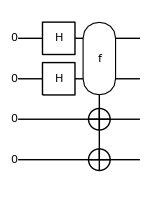

```mathematica
cc={1,2};
tt={3,4};
qc=QuantumCircuit[Ket[Join[S@cc,S@tt]],S[cc,6],Oracle[f,S@cc,S@tt]]
```

The output state is an entangled state (unless the classical oracle f is constant).

```mathematica
out=ExpressionFor[qc]
```

1/2 0_S_10_S_21_S_31_S_4+1/2 0_S_11_S_21_S_30_S_4+1/2 1_S_10_S_20_S_31_S_4+1/2 1_S_11_S_20_S_30_S_4

To make clearer the copies made tot the ancillary register, it may be useful to rewrite the state vector in a form that distinguishes the native and ancillary register.

```mathematica
KetFactor[out,S@cc]
```

0_S_10_S_2⊗(1/2 1_S_31_S_4)+0_S_11_S_2⊗(1/2 1_S_30_S_4)+1_S_10_S_2⊗(1/2 0_S_31_S_4)+1_S_11_S_2⊗(1/2 0_S_30_S_4)

This is an interesting twist of the quantum oracle. It is useful in Grover’s search algorithm.

The classical oracle mark the solutions, {0,0}=0 and {1,1}=1 in this particular case.

```mathematica
Clear[f];
f[0,0]=1;f[0,1]=0;f[1,0]=0;f[1,1]=1;
```

This quantum circuit model implements the desired mapping.

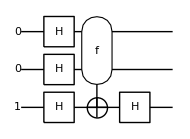

```mathematica
cc={1,2};
tt={3};
ct=Join[cc,tt];
qc=QuantumCircuit[Ket[S[tt]->1,S[ct]],S[ct,6],Oracle[f,S@cc,S@tt],S[tt,6]]
```

```mathematica
out=ExpressionFor[qc];
KetFactor[out,S[tt]]
```

-1/2 (0_S_1-1_S_1)⊗(0_S_2-1_S_2)⊗1_S_3

Check the result.

```mathematica
bs=Basis[S@cc];
ff=f@@@IntegerDigits[Range[0,2^2-1],2,2];
Thread[bs->Power[-1,ff]]
```

{0_S_10_S_2→-1,0_S_11_S_2→1,1_S_10_S_2→1,1_S_11_S_2→-1}

```mathematica
new=bs.Power[-1,ff]/2
```

1/2 (-0_S_10_S_2+0_S_11_S_2+1_S_10_S_2-1_S_11_S_2)

### Deutsch-Jozsa Algorithm

Consider a balanced function as an example.

```mathematica
Clear[f];
f[0,0]=f[1,1]=0;
f[0,1]=f[1,0]=1;
```

Here is a quantum circuit model of the Deutsch-Jozsa algorithm. The final Hadamard gate on the third qubit is not necessary, but we put it here to make the output state more readable.

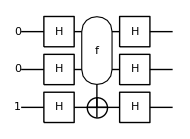

```mathematica
cc={1,2};
tt={3};
all={1,2,3};
qc=QuantumCircuit[Ket[S[3]->1,S@all],S[all,6],Oracle[f,S@cc,S@tt],S[all,6]]
```

```mathematica
out=ExpressionFor[qc]
```

1_S_11_S_21_S_3

### Bernstein-Vazirani Algorithm

Consider a secrete string of bits. The task is to find the secrete string.

```mathematica
string={0,1};
```

In the Bernstein-Vazirani algorithm, the value of the classical oracle f is determined by the given secrete string.

```mathematica
Clear[f];
f[x__]:=Mod[{x}.string,2]
```

For example, f[1,1]=0·1 + 1·1=1.

```mathematica
f[1,1]
```

1

Here is a quantum circuit of the Bernstein-Vazirani algorithm. The final Hadamard gate on the third qubit is not necessary, and we put it here to make the output state more readable.

```mathematica
cc={1,2};
tt={3};
all={1,2,3};
qc=QuantumCircuit[Ket[S[3]->1,S@all],S[all,6],Oracle[f,S@cc,S@tt],S[all,6]]
```

-Graphics-

```mathematica
out=ExpressionFor[qc]
```

0_S_11_S_21_S_3

Here is the secrete string successfully retrieved.

```mathematica
answer=out[S@cc]
```

{0,1}

### Simon’s Algorithm

Consider again a secrete bit string.

```mathematica
string={1,1};
```

Consider a two-to-one function obeying the rule (specified in Simon’s problem).

```mathematica
Clear[f];
f[0,0]=f[1,1]={0,1};
f[0,1]=f[1,0]={1,1};
```

Here is an implementation of the corresponding quantum oracle.

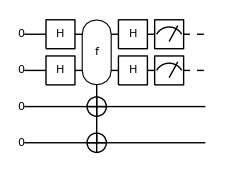

```mathematica
cc={1,2};
tt={3,4};
all=Join[cc,tt];
qc=QuantumCircuit[Ket[S@all],S[cc,6],Oracle[f,S@cc,S@tt],S[cc,6],Measurement[S[cc,3]]]
```

```mathematica
out=ExpressionFor[qc]
result=Readout[S[cc,3]]
```

(0_S_10_S_20_S_31_S_4)/(√2)+(0_S_10_S_21_S_31_S_4)/(√2)

{0,0}

```mathematica
eqs=Table[ExpressionFor[Matrix[qc],S@all];Readout[S[cc,3]],{4}]
```

{{0,0},{0,0},{0,0},{0,0}}

Now let us examine a lager system. Suppose that we are given a secrete bit string.

```mathematica
string={1,1,0};
```

This is a function consistent with the above secrete bit string.

```mathematica
Clear[f];
f[0,0,0]=f[1,1,0]={0,1,1};
f[0,0,1]=f[1,1,1]={1,1,1};
f[0,1,0]=f[1,0,0]={1,0,0};
f[0,1,1]=f[1,0,1]={0,0,1};
```

Here is an implementation of the corresponding quantum oracle.

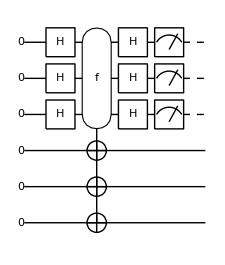

```mathematica
cc={1,2,3};
tt={4,5,6};
all=Join[cc,tt];
qc1=QuantumCircuit[Ket[S@all],S[cc,6],Oracle[f,S@cc,S@tt],S[cc,6]];
qc2=QuantumCircuit[qc1,Measurement[S[cc,3]]]
```

This is one way to get the measurement outcome.

```mathematica
out=ExpressionFor[qc2]
result=Readout[S[cc,3]]
```

-1/2 0_S_10_S_21_S_30_S_40_S_51_S_6+1/2 0_S_10_S_21_S_30_S_41_S_51_S_6+1/2 0_S_10_S_21_S_31_S_40_S_50_S_6-1/2 0_S_10_S_21_S_31_S_41_S_51_S_6

{0,0,1}

To make repeated measurements, it is more efficient to first compute the state just before the measurement.

```mathematica
new=ExpressionFor[qc1];
```

Now we perform the measurement repeatedly.

```mathematica
data=Table[Measurement[S[cc,3]]@new;Readout[S[cc,3]],{12}];
data//TableForm
```

1 | 1 | 0
1 | 1 | 0
0 | 0 | 0
1 | 1 | 1
1 | 1 | 1
0 | 0 | 0
0 | 0 | 1
0 | 0 | 0
0 | 0 | 0
1 | 1 | 1
0 | 0 | 1
0 | 0 | 1

As two linearly independent vectors (bit strings), we choose these:

```mathematica
mat={{1,1,0},{0,0,1}}
```

{{1,1,0},{0,0,1}}

Then, the linear equation, mat.ss=0 (mod 2), for the Boolean variables ss:={s1,s2,s3} is given by the following, which agrees with the given secrete bit string.

```mathematica
ss={1,1,0}
```

{1,1,0}

```mathematica
Mod[mat.ss,2]
```

{0,0}

## Quantum Fourier Transform

### Definition and Physical Meaning

### Quantum Implementation

Here we simulate the quantum Fourier transform on a quantum register of 4 qubits.

```mathematica
$n=4;
```

Here defined are the controlled-phase gates.

```mathematica
CP[j_,j_]:=S[j,6]
CP[j_,k_]:=ControlledGate[S[j],S[k,C[k-j-1]],"Label"->Subscript["T",j-k]]/;j>k
CP[j_,k_]:=ControlledGate[S[j],S[k,C[j-k-1]],"Label"->Subscript["T",k-j]]/;j<k
```

We denote by the label T_k the relative phase shift by π/2^k: T_k:=(1 | 0
0 | e^(iπ/2^k)).

This is just a short-hand function.

```mathematica
SW[j_]:=SWAP[S[j],S[$n-j+1]]
SW[All]:=Table[SW[j],{j,1,$n/2}]
```

This is the standard implementation, which can be seen commonly in textbooks.

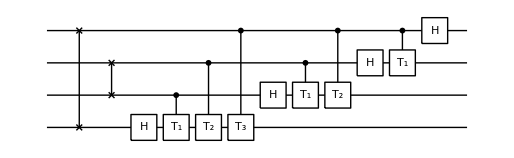

```mathematica
gates=Flatten@Table[CP[j,k],{k,$n,1,-1},{j,k,1,-1}];
qc1=QuantumCircuit[Sequence@@SW[All],Sequence@@gates]
```

To verify the above quantum circuit model, we compare its matrix representation with the matrix for the discrete Fourier transform.

```mathematica
mat=Matrix[qc1]//TrigToExp;
new=FourierMatrix[Power[2,$n]];
DeleteCases[new-mat//Simplify//Flatten,0]
```

{}

One can also reverse the order of qubits later to get the following quantum circuit model for the quantum Fourier transform.

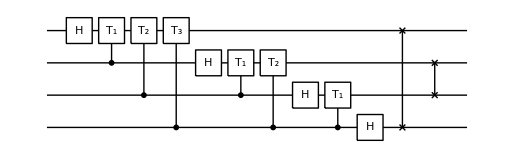

```mathematica
gates=Flatten@Table[CP[j,k],{k,1,$n},{j,k,$n}];
qc2=QuantumCircuit[Sequence@@gates,Sequence@@SW[All]]
```

Again, verify it by comparing the matrix representation with the matrix for the discrete Fourier transform.

```mathematica
mat=Matrix[qc2]//TrigToExp;
new=FourierMatrix[Power[2,$n]];
DeleteCases[new-mat//Simplify//Flatten,0]
```

{}

### Semiclassical Implementation

Here, we simulate the semiclassical implementation of the quantum Fourier transform. Again, we consider a quantum register of four qubits.

```mathematica
$n=4;
SS=S[Range[$n],$];
```

Let us first define the controlled-phase gates.

```mathematica
CP[j_,j_]:=S[j,6]
CP[j_,k_]:=ControlledGate[S[j],S[k,C[k-j-1]],"Label"->Subscript["T",j-k]]/;j>k
CP[j_,k_]:=ControlledGate[S[j],S[k,C[j-k-1]],"Label"->Subscript["T",k-j]]/;j<k
```

```mathematica
in=Ket@@Thread[SS->RandomChoice[{0,1},$n]]
```

0_S_10_S_20_S_31_S_4

This is a quantum circuit model for the quantum Fourier transformation.

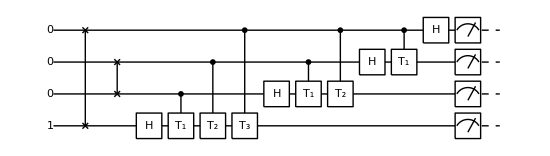

```mathematica
gates=Flatten@Table[CP[j,k],{k,$n,1,-1},{j,k,1,-1}];
swaps=Table[SWAP[S[k],S[$n-k+1]],{k,1,$n/2}];
qc1=QuantumCircuit[in,Sequence@@swaps,Sequence@@gates,Measurement@Through[SS[3]]]
```

This is the semiclassical implementation of the quantum Fourier transform.

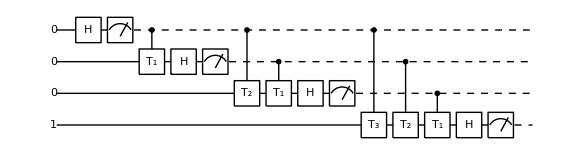

```mathematica
gates=Table[CP[j,k],{k,1,$n},{j,1,k}];
gates=Flatten@MapIndexed[Append[#1,Measurement@S[#2,3]]&,gates];
swaps=Table[SWAP[S[k],S[$n-k+1]],{k,1,$n/2}];
qc2=QuantumCircuit[in,Sequence@@gates]
```

To verify the equivalence of the two quantum circuit models, we compare the probability distributions.

```mathematica
EchoTiming[data1=Table[ExpressionFor[qc1];FromDigits[Readout@Through[SS[3]],2],{500}];]
```

42.1714

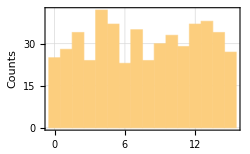

```mathematica
Histogram[data1,FrameLabel->{"Measurement Outcome","Counts"}]
```

Note that the bit strings of the measurement outcomes from the semiclassical model must be reversed .

```mathematica
EchoTiming[data2=Table[ExpressionFor[qc2];FromDigits[Reverse@Readout@Through[SS[3]],2],{500}];]
```

15.0392

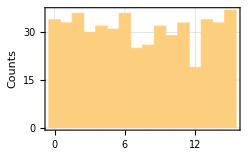

```mathematica
Histogram[data2,FrameLabel->{"Measurement Outcome","Counts"}]
```

The discrepancy between the two distributions is due to the finite sample size.

Another way to test the equivalence of the fully quantum and semiclassical implementation of the quantum Fourier transformation is to take as the input state one that ends up in a product state.

```mathematica
vecs=FourierMatrix[Power[2,$n],FourierParameters->{0,-1}].Basis[SS];
in=RandomChoice[vecs]
```

1/4 0_S_10_S_20_S_30_S_4+1/4 ⅇ^(-(ⅈ π)/4) 0_S_10_S_20_S_31_S_4-1/4 ⅈ 0_S_10_S_21_S_30_S_4+1/4 ⅇ^(-(3 ⅈ π)/4) 0_S_10_S_21_S_31_S_4-1/4 0_S_11_S_20_S_30_S_4+1/4 ⅇ^((3 ⅈ π)/4) 0_S_11_S_20_S_31_S_4+1/4 ⅈ 0_S_11_S_21_S_30_S_4+1/4 ⅇ^((ⅈ π)/4) 0_S_11_S_21_S_31_S_4+1/4 1_S_10_S_20_S_30_S_4+1/4 ⅇ^(-(ⅈ π)/4) 1_S_10_S_20_S_31_S_4-1/4 ⅈ 1_S_10_S_21_S_30_S_4+1/4 ⅇ^(-(3 ⅈ π)/4) 1_S_10_S_21_S_31_S_4-1/4 1_S_11_S_20_S_30_S_4+1/4 ⅇ^((3 ⅈ π)/4) 1_S_11_S_20_S_31_S_4+1/4 ⅈ 1_S_11_S_21_S_30_S_4+1/4 ⅇ^((ⅈ π)/4) 1_S_11_S_21_S_31_S_4

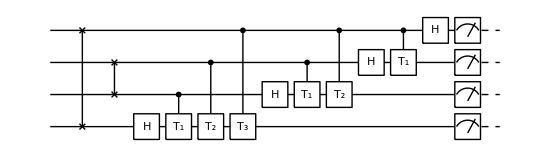

```mathematica
gates=Flatten@Table[CP[j,k],{k,$n,1,-1},{j,k,1,-1}];
swaps=Table[SWAP[S[k],S[$n-k+1]],{k,1,$n/2}];
qc1=QuantumCircuit[{in,"Label"->None},Sequence@@swaps,Sequence@@gates,Measurement@Through[SS[3]]]
```

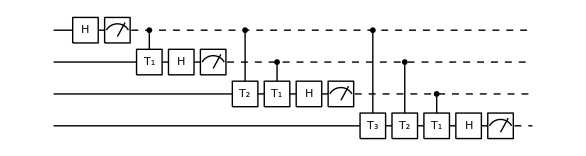

```mathematica
gates=Table[CP[j,k],{k,1,$n},{j,1,k}];
gates=Flatten@MapIndexed[Append[#1,Measurement@S[#2,3]]&,gates];
swaps=Table[SWAP[S[k],S[$n-k+1]],{k,1,$n/2}];
qc2=QuantumCircuit[{in,"Label"->None},Sequence@@gates]
```

```mathematica
out1=ExpressionFor[qc1]
```

0_S_10_S_21_S_30_S_4

Again, recall that the order of qubits are reversed in the semiclassical implementation.

```mathematica
out2=ExpressionFor[qc2]
```

0_S_11_S_20_S_30_S_4

## Quantum Phase Estimation

### Definition

### Implementation

We take an ancillary register consisting of four qubits, which we call the “probe” register.

```mathematica
$m=4; (* the number of qubits in the "probe" register *)
prb=Range[$m]; (* the "probe" register *)
sys=$m+1; (* the "system" register *)
```

We consider a rotation around the z-axis for the unitary operator. In this case, the logical basis consists of the eigenstates of the unitary operator.

```mathematica
ϕ=18/25;
```

Here is the controlled-U^(2^(m-j)) operator to be used in the phase estimation algorithm.

```mathematica
Clear[ctrlU]
ctrlU[j_]:=ControlledGate[S[j],Phase[-2Pi ϕ*Power[2,$m-j],S[sys,3]],"Label"->Superscript["U",Superscript["2",ToString[$m-j]]],
"LabelSize"->0.65]
```

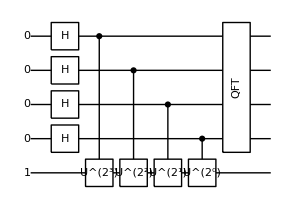

```mathematica
qc=QuantumCircuit[Ket[S@prb],Ket[S[sys]->1],{S[prb,6],"LabelSize"->0.8},ctrlU[1],ctrlU[2],ctrlU[3],ctrlU[4],QFT[S@prb]]
```

In this particular example, we already know that the “system” register remains in its initial state and what the initial state is. To make the process general, however, we take the partial trace over the system register to focus on the “probe” register.

```mathematica
out=Matrix[N@qc];
rho=PartialTrace[out,{sys}];
```

From the density matrix of the probe register, we can get the probability to read out the possible values of the normalized phase.

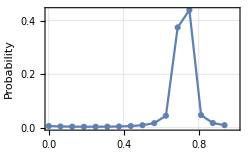

```mathematica
probability=Transpose@{Range[0,2^$m-1]/2^$m,Normal@Chop@Diagonal@rho};g=ListLinePlot[probability,PlotRange->{{0,1},All},PlotMarkers->Automatic,
FrameLabel->{"ϕ","Probability"}]
```

### Accuracy

### Simulation of von Neumann Measurement

## Applications

### The Period-Finding Algorithm

We demonstrate the basic ideas in the period-finding algorithm. More complete example follows below.

```mathematica
$n=4;
$N=Power[2,$n];
```

We take an example of the modular exponential function, f(x)=a^x (mod L) for a fixed a and L. Here a and L are assumed to be co-primes.

```mathematica
$a=3;
Clear[f];
f[k_]:=PowerMod[$a,k,$N]
```

The function is periodic.

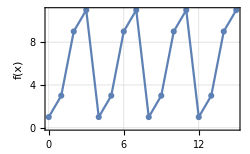

```mathematica
ListPlot[Table[{k,f[k]},{k,0,$N-1}],Joined->True,PlotMarkers->Automatic,FrameLabel->{"x",HoldForm@f[x]}]
```

The classical oracle (in the binary form) corresponding to the function f (expressed in usual integers).

```mathematica
Clear[g]
g[x__]:=IntegerDigits[f[FromDigits[{x},2]],2,$n]
```

Here is the quantum circuit model of the algorithm.

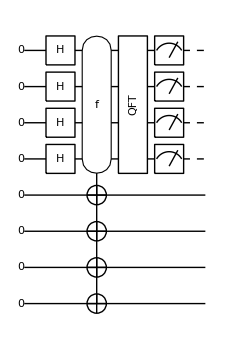

```mathematica
cc=Range[$n];
tt=Range[$n+1,$n+$n];
qc0=QuantumCircuit[Ket[Join[S@cc,S@tt]],S[cc,6],Oracle[g,S@cc,S@tt],
QFT[S@cc]];
qc=QuantumCircuit[qc0,Measurement@S[cc,3]]
```

```mathematica
EchoTiming[out=ExpressionFor[qc]]
result=Readout@S[cc,3]
```

2.90992

1/2 1_S_10_S_20_S_30_S_40_S_50_S_60_S_71_S_8-1/2 1_S_10_S_20_S_30_S_40_S_50_S_61_S_71_S_8+1/2 1_S_10_S_20_S_30_S_41_S_50_S_60_S_71_S_8-1/2 1_S_10_S_20_S_30_S_41_S_50_S_61_S_71_S_8

{1,0,0,0}

From the measurement outcome, one can find the period. In this case, the period is 4.

```mathematica
frac=FromDigits[result,2]/$N
```

1/2

For a more complete overview, let us examine all possible outcomes.

```mathematica
EchoTiming[new=ExpressionFor[qc0]]
```

1.98759

1/4 0_S_10_S_20_S_30_S_40_S_50_S_60_S_71_S_8+1/4 0_S_10_S_20_S_30_S_40_S_50_S_61_S_71_S_8+1/4 0_S_10_S_20_S_30_S_41_S_50_S_60_S_71_S_8+1/4 0_S_10_S_20_S_30_S_41_S_50_S_61_S_71_S_8+1/4 0_S_11_S_20_S_30_S_40_S_50_S_60_S_71_S_8+1/4 ⅈ 0_S_11_S_20_S_30_S_40_S_50_S_61_S_71_S_8-1/4 0_S_11_S_20_S_30_S_41_S_50_S_60_S_71_S_8-1/4 ⅈ 0_S_11_S_20_S_30_S_41_S_50_S_61_S_71_S_8+1/4 1_S_10_S_20_S_30_S_40_S_50_S_60_S_71_S_8-1/4 1_S_10_S_20_S_30_S_40_S_50_S_61_S_71_S_8+1/4 1_S_10_S_20_S_30_S_41_S_50_S_60_S_71_S_8-1/4 1_S_10_S_20_S_30_S_41_S_50_S_61_S_71_S_8+1/4 1_S_11_S_20_S_30_S_40_S_50_S_60_S_71_S_8-1/4 ⅈ 1_S_11_S_20_S_30_S_40_S_50_S_61_S_71_S_8-1/4 1_S_11_S_20_S_30_S_41_S_50_S_60_S_71_S_8+1/4 ⅈ 1_S_11_S_20_S_30_S_41_S_50_S_61_S_71_S_8

```mathematica
data=Table[Measurement[S[cc,3]]@new;FromDigits[Readout[S[cc,3]],2],{15}]
```

{4,0,12,8,8,0,4,12,0,4,12,0,4,4,0}

```mathematica
sec=Union[data/$N]
```

{0,1/4,1/2,3/4}

The period must be 4, which agrees with the true value.

Now we consider a full period-finding problem. We consider a four-qubit system.

```mathematica
$n=4;
$N=Power[2,$n];
```

We define an arbitrary function with period 3.

```mathematica
Clear[f];
f[0]=1;f[1]=5;f[2]=4;
f[x_]:=f[Mod[x,3]]
```

This plot illustrates that the function is indeed periodic with period 3.

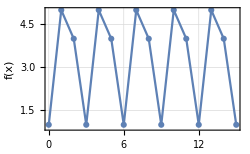

```mathematica
ListPlot[Table[{k,f[k]},{k,0,$N-1}],Joined->True,PlotMarkers->Automatic,FrameLabel->{"x",HoldForm@f[x]}]
```

The classical oracle (in the binary form) corresponding to the function f (expressed in usual integers).

```mathematica
Clear[g]
g[x__]:=IntegerDigits[f[FromDigits[{x},2]],2,$n]
```

Here is the quantum circuit model of the algorithm.

```mathematica
cc=Range[$n];
tt=Range[$n+1,$n+$n];
qc0=QuantumCircuit[Ket[Join[S@cc,S@tt]],S[cc,6],Oracle[g,S@cc,S@tt],
QFT[S@cc,N->True]];
qc=QuantumCircuit[qc0,Measurement@S[cc,3]]
```

-Graphics-

This is a full run of the above quantum circuit model.

```mathematica
EchoTiming[out=ExpressionFor[qc];]
result=Readout@S[cc,3]
```

4.46242

{1,0,1,1}

In order to check more random results, it is more efficient to first calculate the output state right before the measurement.

```mathematica
EchoTiming[new=ExpressionFor[qc0];]
```

3.4865

From the above output state, we perform measurements (as many times as we like) to get random results.

```mathematica
out=Measurement[S[cc,3]]@N[new];
phi=FromDigits[Readout@S[cc,3],2]/$N
```

5/16

From the above random result, we determine the period of the function by utilizing the continued fraction representation of the estimated phase.

```mathematica
cnt=ContinuedFraction[phi]
candidates=Convergents[cnt]
```

{0,3,5}

{0,1/3,5/16}

From the above convergents, we have two candidates 3 (and its multiples 6, 9, 12, 15 are also candidates) and 16. Evaluation of the function for some arguments confirms that 3 is the period of the function.

### The Order-Finding Algorithm

### Quantum Factorization Algorithm

### Quantum Search Algorithm

Here is a quantum circuit model for Grover’s diffusion operator.

We first implement (1-200).

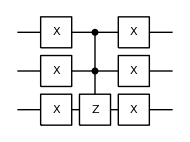

```mathematica
$n=3;
jj=Range[$n];
ss=S[jj,$];
cz=CZ@@@Subsets[ss,{2}];
cz=Successive[CZ,ss];
cz=CZ[S[1],#]&/@Rest@ss;
qc=QuantumCircuit[S[jj,1],
ControlledGate[S[Most@jj],S[$n,3]],
S[jj,1]]
```

```mathematica
bs=Basis[S[jj]];
out=qc**bs;
Thread[bs->out]//TableForm
```

0_S_10_S_20_S_3→-0_S_10_S_20_S_3
0_S_10_S_21_S_3→0_S_10_S_21_S_3
0_S_11_S_20_S_3→0_S_11_S_20_S_3
0_S_11_S_21_S_3→0_S_11_S_21_S_3
1_S_10_S_20_S_3→1_S_10_S_20_S_3
1_S_10_S_21_S_3→1_S_10_S_21_S_3
1_S_11_S_20_S_3→1_S_11_S_20_S_3
1_S_11_S_21_S_3→1_S_11_S_21_S_3

This is Grover’s diffusion operator (up to an irrelevant global phase factor of -1).

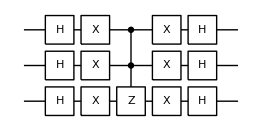

```mathematica
qc1=QuantumCircuit[S[jj,6],qc,S[jj,6]]
```

Here we demonstrate the quantum search algorithm.

We work with 4 (system) qubits and one ancillary qubit. The ancillary qubit is for the quantum oracle.

```mathematica
$n=4;
cc=Range[$n-1];
tt=$n;
jj=Range[$n];
aa=$n+1;
```

Here we specify a classical oracle. The function f is more human readable. The function g will be used in the actual quantum oracle.

```mathematica
Clear[f]
f[3]=1;f[_]=0;
g[x__]:=f@FromDigits[{x},2]
```

The ancilla qubit is prepared in the following state.

```mathematica
in=ProductState[S[aa]->{1,-1}/Sqrt[2]];
in//Elaborate
```

(0_S_5)/(√2)-(1_S_5)/(√2)

This is a quantum circuit for the Grover rotation.

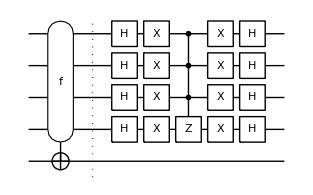

```mathematica
grv=QuantumCircuit[
Oracle[g,S[jj],S[aa]],"Separator",
S[jj,6],S[jj,1],ControlledGate[S[cc],S[tt,3]],S[jj,1],S[jj,6],
"PortSize"->{0.5,0.2}
]
```

We apply the Grover rotation once on the input state.

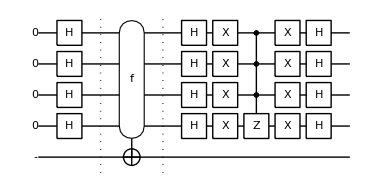

```mathematica
qc1=QuantumCircuit[Ket[S[jj]],{in,"Label"->"-"},S[jj,6],"Separator",grv]
```

Here is the result of it.

```mathematica
out1=Elaborate[qc1]
```

-(3 0_S_10_S_20_S_30_S_40_S_5)/(16 √2)+(3 0_S_10_S_20_S_30_S_41_S_5)/(16 √2)-(3 0_S_10_S_20_S_31_S_40_S_5)/(16 √2)+(3 0_S_10_S_20_S_31_S_41_S_5)/(16 √2)-(3 0_S_10_S_21_S_30_S_40_S_5)/(16 √2)+(3 0_S_10_S_21_S_30_S_41_S_5)/(16 √2)-(11 0_S_10_S_21_S_31_S_40_S_5)/(16 √2)+(11 0_S_10_S_21_S_31_S_41_S_5)/(16 √2)-(3 0_S_11_S_20_S_30_S_40_S_5)/(16 √2)+(3 0_S_11_S_20_S_30_S_41_S_5)/(16 √2)-(3 0_S_11_S_20_S_31_S_40_S_5)/(16 √2)+(3 0_S_11_S_20_S_31_S_41_S_5)/(16 √2)-(3 0_S_11_S_21_S_30_S_40_S_5)/(16 √2)+(3 0_S_11_S_21_S_30_S_41_S_5)/(16 √2)-(3 0_S_11_S_21_S_31_S_40_S_5)/(16 √2)+(3 0_S_11_S_21_S_31_S_41_S_5)/(16 √2)-(3 1_S_10_S_20_S_30_S_40_S_5)/(16 √2)+(3 1_S_10_S_20_S_30_S_41_S_5)/(16 √2)-(3 1_S_10_S_20_S_31_S_40_S_5)/(16 √2)+(3 1_S_10_S_20_S_31_S_41_S_5)/(16 √2)-(3 1_S_10_S_21_S_30_S_40_S_5)/(16 √2)+(3 1_S_10_S_21_S_30_S_41_S_5)/(16 √2)-(3 1_S_10_S_21_S_31_S_40_S_5)/(16 √2)+(3 1_S_10_S_21_S_31_S_41_S_5)/(16 √2)-(3 1_S_11_S_20_S_30_S_40_S_5)/(16 √2)+(3 1_S_11_S_20_S_30_S_41_S_5)/(16 √2)-(3 1_S_11_S_20_S_31_S_40_S_5)/(16 √2)+(3 1_S_11_S_20_S_31_S_41_S_5)/(16 √2)-(3 1_S_11_S_21_S_30_S_40_S_5)/(16 √2)+(3 1_S_11_S_21_S_30_S_41_S_5)/(16 √2)-(3 1_S_11_S_21_S_31_S_40_S_5)/(16 √2)+(3 1_S_11_S_21_S_31_S_41_S_5)/(16 √2)

We apply the Grover rotation again on the above output state.

```mathematica
qc2=QuantumCircuit[{out1,"Label"->"ψ"},grv]
```

-Graphics-

```mathematica
out2=Elaborate[qc2]
```

(5 0_S_10_S_20_S_30_S_40_S_5)/(64 √2)-(5 0_S_10_S_20_S_30_S_41_S_5)/(64 √2)+(5 0_S_10_S_20_S_31_S_40_S_5)/(64 √2)-(5 0_S_10_S_20_S_31_S_41_S_5)/(64 √2)+(5 0_S_10_S_21_S_30_S_40_S_5)/(64 √2)-(5 0_S_10_S_21_S_30_S_41_S_5)/(64 √2)+(61 0_S_10_S_21_S_31_S_40_S_5)/(64 √2)-(61 0_S_10_S_21_S_31_S_41_S_5)/(64 √2)+(5 0_S_11_S_20_S_30_S_40_S_5)/(64 √2)-(5 0_S_11_S_20_S_30_S_41_S_5)/(64 √2)+(5 0_S_11_S_20_S_31_S_40_S_5)/(64 √2)-(5 0_S_11_S_20_S_31_S_41_S_5)/(64 √2)+(5 0_S_11_S_21_S_30_S_40_S_5)/(64 √2)-(5 0_S_11_S_21_S_30_S_41_S_5)/(64 √2)+(5 0_S_11_S_21_S_31_S_40_S_5)/(64 √2)-(5 0_S_11_S_21_S_31_S_41_S_5)/(64 √2)+(5 1_S_10_S_20_S_30_S_40_S_5)/(64 √2)-(5 1_S_10_S_20_S_30_S_41_S_5)/(64 √2)+(5 1_S_10_S_20_S_31_S_40_S_5)/(64 √2)-(5 1_S_10_S_20_S_31_S_41_S_5)/(64 √2)+(5 1_S_10_S_21_S_30_S_40_S_5)/(64 √2)-(5 1_S_10_S_21_S_30_S_41_S_5)/(64 √2)+(5 1_S_10_S_21_S_31_S_40_S_5)/(64 √2)-(5 1_S_10_S_21_S_31_S_41_S_5)/(64 √2)+(5 1_S_11_S_20_S_30_S_40_S_5)/(64 √2)-(5 1_S_11_S_20_S_30_S_41_S_5)/(64 √2)+(5 1_S_11_S_20_S_31_S_40_S_5)/(64 √2)-(5 1_S_11_S_20_S_31_S_41_S_5)/(64 √2)+(5 1_S_11_S_21_S_30_S_40_S_5)/(64 √2)-(5 1_S_11_S_21_S_30_S_41_S_5)/(64 √2)+(5 1_S_11_S_21_S_31_S_40_S_5)/(64 √2)-(5 1_S_11_S_21_S_31_S_41_S_5)/(64 √2)

We repeat the same procedure.

```mathematica
qc3=QuantumCircuit[{out2,"Label"->"ψ"},grv]
```

-Graphics-

```mathematica
out3=Elaborate[qc3]
```

(13 0_S_10_S_20_S_30_S_40_S_5)/(256 √2)-(13 0_S_10_S_20_S_30_S_41_S_5)/(256 √2)+(13 0_S_10_S_20_S_31_S_40_S_5)/(256 √2)-(13 0_S_10_S_20_S_31_S_41_S_5)/(256 √2)+(13 0_S_10_S_21_S_30_S_40_S_5)/(256 √2)-(13 0_S_10_S_21_S_30_S_41_S_5)/(256 √2)-(251 0_S_10_S_21_S_31_S_40_S_5)/(256 √2)+(251 0_S_10_S_21_S_31_S_41_S_5)/(256 √2)+(13 0_S_11_S_20_S_30_S_40_S_5)/(256 √2)-(13 0_S_11_S_20_S_30_S_41_S_5)/(256 √2)+(13 0_S_11_S_20_S_31_S_40_S_5)/(256 √2)-(13 0_S_11_S_20_S_31_S_41_S_5)/(256 √2)+(13 0_S_11_S_21_S_30_S_40_S_5)/(256 √2)-(13 0_S_11_S_21_S_30_S_41_S_5)/(256 √2)+(13 0_S_11_S_21_S_31_S_40_S_5)/(256 √2)-(13 0_S_11_S_21_S_31_S_41_S_5)/(256 √2)+(13 1_S_10_S_20_S_30_S_40_S_5)/(256 √2)-(13 1_S_10_S_20_S_30_S_41_S_5)/(256 √2)+(13 1_S_10_S_20_S_31_S_40_S_5)/(256 √2)-(13 1_S_10_S_20_S_31_S_41_S_5)/(256 √2)+(13 1_S_10_S_21_S_30_S_40_S_5)/(256 √2)-(13 1_S_10_S_21_S_30_S_41_S_5)/(256 √2)+(13 1_S_10_S_21_S_31_S_40_S_5)/(256 √2)-(13 1_S_10_S_21_S_31_S_41_S_5)/(256 √2)+(13 1_S_11_S_20_S_30_S_40_S_5)/(256 √2)-(13 1_S_11_S_20_S_30_S_41_S_5)/(256 √2)+(13 1_S_11_S_20_S_31_S_40_S_5)/(256 √2)-(13 1_S_11_S_20_S_31_S_41_S_5)/(256 √2)+(13 1_S_11_S_21_S_30_S_40_S_5)/(256 √2)-(13 1_S_11_S_21_S_30_S_41_S_5)/(256 √2)+(13 1_S_11_S_21_S_31_S_40_S_5)/(256 √2)-(13 1_S_11_S_21_S_31_S_41_S_5)/(256 √2)

In this case, the optimal number of applications of the Grover algorithm is four. So, this is supposed to be the last step.

```mathematica
qc4=QuantumCircuit[{out3,"Label"->"ψ"},grv]
```

-Graphics-

This is the final state.

```mathematica
out4=Elaborate[qc4]
```

-(171 0_S_10_S_20_S_30_S_40_S_5)/(1024 √2)+(171 0_S_10_S_20_S_30_S_41_S_5)/(1024 √2)-(171 0_S_10_S_20_S_31_S_40_S_5)/(1024 √2)+(171 0_S_10_S_20_S_31_S_41_S_5)/(1024 √2)-(171 0_S_10_S_21_S_30_S_40_S_5)/(1024 √2)+(171 0_S_10_S_21_S_30_S_41_S_5)/(1024 √2)+(781 0_S_10_S_21_S_31_S_40_S_5)/(1024 √2)-(781 0_S_10_S_21_S_31_S_41_S_5)/(1024 √2)-(171 0_S_11_S_20_S_30_S_40_S_5)/(1024 √2)+(171 0_S_11_S_20_S_30_S_41_S_5)/(1024 √2)-(171 0_S_11_S_20_S_31_S_40_S_5)/(1024 √2)+(171 0_S_11_S_20_S_31_S_41_S_5)/(1024 √2)-(171 0_S_11_S_21_S_30_S_40_S_5)/(1024 √2)+(171 0_S_11_S_21_S_30_S_41_S_5)/(1024 √2)-(171 0_S_11_S_21_S_31_S_40_S_5)/(1024 √2)+(171 0_S_11_S_21_S_31_S_41_S_5)/(1024 √2)-(171 1_S_10_S_20_S_30_S_40_S_5)/(1024 √2)+(171 1_S_10_S_20_S_30_S_41_S_5)/(1024 √2)-(171 1_S_10_S_20_S_31_S_40_S_5)/(1024 √2)+(171 1_S_10_S_20_S_31_S_41_S_5)/(1024 √2)-(171 1_S_10_S_21_S_30_S_40_S_5)/(1024 √2)+(171 1_S_10_S_21_S_30_S_41_S_5)/(1024 √2)-(171 1_S_10_S_21_S_31_S_40_S_5)/(1024 √2)+(171 1_S_10_S_21_S_31_S_41_S_5)/(1024 √2)-(171 1_S_11_S_20_S_30_S_40_S_5)/(1024 √2)+(171 1_S_11_S_20_S_30_S_41_S_5)/(1024 √2)-(171 1_S_11_S_20_S_31_S_40_S_5)/(1024 √2)+(171 1_S_11_S_20_S_31_S_41_S_5)/(1024 √2)-(171 1_S_11_S_21_S_30_S_40_S_5)/(1024 √2)+(171 1_S_11_S_21_S_30_S_41_S_5)/(1024 √2)-(171 1_S_11_S_21_S_31_S_40_S_5)/(1024 √2)+(171 1_S_11_S_21_S_31_S_41_S_5)/(1024 √2)

To analyze the result, we ignore the ancillary qubit. Note that the result is a density matrix.

```mathematica
new=Matrix@PartialTrace[out4,S[aa]];
```

The diagonal elements of the density matrix are the probability in the logical basis.

```mathematica
prb=Diagonal[new];
```

As you can see below, the probability for x=3 is the highest. We conclude that the quantum search algorithm works reasonably well.

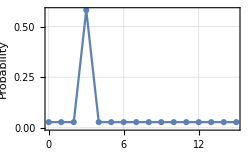

```mathematica
ListLinePlot[Transpose@{Range[0,2^$n-1],prb},
PlotMarkers->Automatic,
FrameLabel->{"x","Probability"}]
```